```mathematica
0.000644 20.7
```

0.0133308

# 2d

```mathematica
xi=0.125;
T=0.1;
h=0;
H=0.1;
Emax=20.7;

nx=3;ny=3;
nxy=nx ny;
t=1.0;
μ=-0.4;
V=2.5;
q=1;
step=0.1;
f[x_]=1/(Exp[x/T]+1);
δ[i_,j_]=KroneckerDelta[i,j];
hpm[i1_,j1_,i2_,j2_,sign_]=-t (If[i1==i2+1&&j1==j2,Exp[-ⅈ q Ax[[i2,j2]]],0]+If[i1==i2-1&&j1==j2,Exp[ⅈ q Ax[[i1,j1]]],0]+If[i1==i2&&j1==j2+1,Exp[-ⅈ q Ay[[i2,j2]]],0]+If[i1==i2&&j1==j2-1,Exp[ⅈ q Ay[[i1,j1]]],0])-(μ+sign*h) δ[i1,i2] δ[j1,j2];
d=Flatten@Table[0.1 Emax (*Tanh[(√((i-nx/2+0.1)^2+(j-ny/2+0.1)^2))/(nx xi)] (i-nx/2+0.1+ⅈ (j-ny/2+0.1))/(√((i-nx/2+0.1)^2+(j-ny/2+0.1)^2))*),{i,nx},{j,ny}];

Ax=Table[0 RandomReal[],{i,nx-1},{j,ny}];
Ay=Table[0 RandomReal[],{i,nx},{j,ny-1}];
Axnew=Ax;Aynew=Ay;
M=Table[0,{i,2 nx ny},{j,2 nx ny}];
ens={};

Do[

Do[M[[j1+ny (i1-1),j2+ny (i2-1)]]=N[hpm[i1,j1,i2,j2,(+1)]],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j1+ny (i1-1)+nx ny,j2+ny (i2-1)+nx ny]]=-N[hpm[i1,j1,i2,j2,(-1)]*],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j+ny (i-1),j+ny (i-1)+nxy]]=N[d[[j+ny (i-1)]]],{i,nx},{j,ny}];
Do[M[[j+ny (i-1)+nxy,j+ny (i-1)]]=N[d[[j+ny (i-1)]]*],{i,nx},{j,ny}];
(*Do[M[[j1+ny (i1-1),j2+ny (i2-1)]]=N[hpm[i1,j1,i2,j2,(+1)]],{i2,nx},{j2,ny},{i1,nx},{j1,ny}];
Do[M[[j1+ny (i1-1)+nx ny,j2+ny (i2-1)+nx ny]]=-N[hpm[i1,j1,i2,j2,(-1)]*],{i2,nx},{j2,ny},{i1,nx},{j1,ny}];
Do[M[[j+ny (i-1),j+ny (i-1)+nxy]]=N[d[[j+ny (i-1)]]],{i,nx},{j,ny}];
Do[M[[j+ny (i-1)+nxy,j+ny (i-1)]]=N[d[[j+ny (i-1)]]*],{i,nx},{j,ny}];*)

{e,evec}=Eigensystem[M];

{evecU,evecV}=Partition[evecᵀ,nxy];
Jx=Table[4 q Im[Sum[ (hpm[i,j,i+1,j,+1] evecU[[j+ny (i),k]] (evecU[[j+ny (i-1),k]]*)+(hpm[i,j,i+1,j,+1]*) evecV[[j+ny (i),k]] (evecV[[j+ny (i-1),k]]*)) f[e[[k]]],{k,2 nxy}]],{i,nx-1},{j,ny}];
Jy=Table[4 q Im[Sum[(hpm[i,j,i,j+1,+1] evecU[[j+1+ny (i-1),k]] (evecU[[j+ny (i-1),k]]*)+(hpm[i,j,i,j+1,+1]*) evecV[[j+1+ny (i-1),k]] (evecV[[j+ny (i-1),k]]*)) f[e[[k]]],{k,2 nxy}]],{i,nx},{j,ny-1}];
Do[Axnew[[i,j]]+=-step (If[j≠ny&&i≠nx,-(Ax[[i,j+1]]-Ax[[i,j]])+(Ay[[i+1,j]]-Ay[[i,j]])-H,0]+If[j≠1&&i≠nx,(Ax[[i,j]]-Ax[[i,j-1]])-(Ay[[i+1,j-1]]-Ay[[i,j-1]])+H,0]-Jx[[i,j]]);,{i,nx-1},{j,ny}];
Do[Aynew[[i,j]]+=-step (If[j≠ny&&i≠nx,(Ax[[i,j+1]]-Ax[[i,j]])-(Ay[[i+1,j]]-Ay[[i,j]])+H,0]+If[j≠ny&&i≠1,-(Ax[[i-1,j+1]]-Ax[[i-1,j]])+(Ay[[i,j]]-Ay[[i-1,j]])-H,0]-Jy[[i,j]]);,{i,nx},{j,ny-1}];
Ax=Axnew;Ay=Aynew;
AppendTo[ens,(d.d*)/V+1/2 Sum[(-(Ax[[i,j+1]]-Ax[[i,j]])+(Ay[[i+1,j]]-Ay[[i,j]])-H)^2,{i,nx-1},{j,ny-1}]-T Total@Log[1+Exp[-Abs[e]/T]]];
,{iter,2}]
B=Table[-(Ax[[i,j+1]]-Ax[[i,j]])+(Ay[[i+1,j]]-Ay[[i,j]]),{i,nx-1},{j,ny-1}];
```

```mathematica
Jx//MatrixForm
```

(-0.0134381 | 1.42471×10^-13 | 0.0134381
-0.0134381 | -1.49084×10^-13 | 0.0134381)

```mathematica
Jy//MatrixForm
```

(0.0134381 | 0.0134381
-1.4262×10^-13 | 1.49007×10^-13
-0.0134381 | -0.0134381)

```mathematica
Ax//MatrixForm
```

(0.0166562 | 1.42471×10^-14 | -0.0166562
0.0166562 | -1.49084×10^-14 | -0.0166562)

```mathematica
Ay//MatrixForm
```

(-0.0166562 | -0.0166562
-1.4262×10^-14 | 1.49007×10^-14
0.0166562 | 0.0166562)

```mathematica
0.019343806241070974/0.01666666
```

1.16063

```mathematica
0.01343806241070971/0.013335
```

1.00773

```mathematica
h=0;
nx=3;ny=3;
nxy=nx ny;
f[x_]=1/(Exp[-x/T]+1);
δ[i_,j_]=KroneckerDelta[i,j];
hpm[i1_,j1_,i2_,j2_,sign_]=-t (If[i1==i2+1&&j1==j2,Exp[-ⅈ q Ax[[i2,j2]]],0]+If[i1==i2-1&&j1==j2,Exp[ⅈ q Ax[[i1,j1]]],0]+If[i1==i2&&j1==j2+1,Exp[-ⅈ q Ay[[i2,j2]]],0]+If[i1==i2&&j1==j2-1,Exp[ⅈ q Ay[[i1,j1]]],0])-(μ+sign*h) δ[i1,i2] δ[j1,j2];
d=Flatten@Table[dd,{i,nx},{j,ny}];
Ax=Table[ax[i,j],{i,nx-1},{j,ny}];
Ay=Table[ay[i,j],{i,nx},{j,ny-1}];
M=Table[0,{i,2 nx ny},{j,2 nx ny}];
Do[M[[j1+ny (i1-1),j2+ny (i2-1)]]=hpm[i1,j1,i2,j2,(+1)],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j1+ny (i1-1)+nx ny,j2+ny (i2-1)+nx ny]]=-hpm[i1,j1,i2,j2,(-1)]*,{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j+ny (i-1),j+ny (i-1)+nxy]]=d[[j+ny (i-1)]],{i,nx},{j,ny}];
Do[M[[j+ny (i-1)+nxy,j+ny (i-1)]]=d[[j+ny (i-1)]],{i,nx},{j,ny}];
M//MatrixForm
```

```mathematica
M[[5+nxy]]
```

{0,0,0,0,dd,0,0,0,0,0,ⅇ^(ⅈ Conjugate[q ax[1,2]]) Conjugate[t],0,ⅇ^(ⅈ Conjugate[q ay[2,1]]) Conjugate[t],Conjugate[μ],ⅇ^(-ⅈ Conjugate[q ay[2,2]]) Conjugate[t],0,ⅇ^(-ⅈ Conjugate[q ax[2,2]]) Conjugate[t],0}

```mathematica
j1+ny (i1-1)/.i1->2/.j1->2
```

5

```mathematica
M-(evecᵀ).DiagonalMatrix[e].(evec*)//Abs//Max
```

2.84217×10^-14

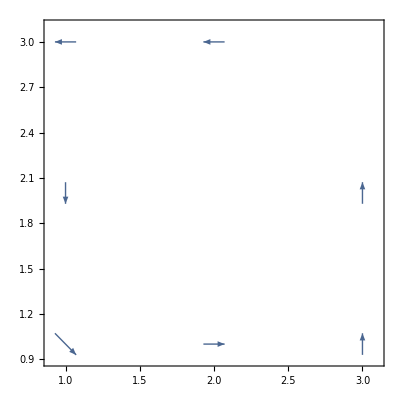

```mathematica
J=Table[{If[i≠nx,Jx[[i,j]],0],If[j≠ny,Jy[[i,j]],0]},{i,nx},{j,ny}];
ListVectorPlot[J,VectorPoints->All]
```

```mathematica
ListPlot[ens,PlotRange->All]
ListPointPlot3D[B,PlotRange->All]
```

```mathematica
Jx=-{{0.013438,0,-0.013438},{0.013438,0,-0.013438}};
Jy=-{{-0.013438,-0.013438},{0,0},{0.013438,0.013438}};
Ax={{0.01,0,-0.01},{0.01,0,-0.01}};
Ay={{-0.01,-0.01},{0,0},{0.01,0.01}};
Axnew={{0.01,0,-0.01},{0.01,0,-0.01}};
Aynew={{-0.01,-0.01},{0,0},{0.01,0.01}};
Do[Axnew[[i,j]]+=-step (If[j≠ny&&i≠nx,-(Ax[[i,j+1]]-Ax[[i,j]])+(Ay[[i+1,j]]-Ay[[i,j]])-H,0]+If[j≠1&&i≠nx,(Ax[[i,j]]-Ax[[i,j-1]])-(Ay[[i+1,j-1]]-Ay[[i,j-1]])+H,0]-Jx[[i,j]]);,{i,nx-1},{j,ny}];
Do[Aynew[[i,j]]+=-step (If[j≠ny&&i≠nx,(Ax[[i,j+1]]-Ax[[i,j]])-(Ay[[i+1,j]]-Ay[[i,j]])+H,0]+If[j≠ny&&i≠1,-(Ax[[i-1,j+1]]-Ax[[i-1,j]])+(Ay[[i,j]]-Ay[[i-1,j]])-H,0]-Jy[[i,j]]);,{i,nx},{j,ny-1}];
Ax=Axnew;Ay=Aynew;
```

```mathematica
Ax//MatrixForm
```

(0.0166562 | 0. | -0.0166562
0.0166562 | 0. | -0.0166562)

```mathematica
Ay//MatrixForm
```

(-0.0033335 | -0.0033335
0. | 0.
0.0033335 | 0.0033335)

```mathematica
ListPlot3D[Flatten[Table[{i+1/2,j+1/2,Abs@d[[j+ny (i-1)]]},{i,nx},{j,ny}],1],InterpolationOrder->0,Filling->Axis,Mesh->None,ColorFunction->"Rainbow",PlotRange->{{1,nx+1},{1,ny+1},All},BoxRatios->{nx,ny,Min[nx,ny]},PlotLegends->Automatic]
```

```mathematica
xi=0.125;
T=0.1;
h=0;
H=0.1;
Emax=20.7;

nx=3;ny=3;
nxy=nx ny;
t=1.0;
μ=-0.4;
V=2.5;
q=1;
step=0.1;
f[x_]=1/(Exp[x/T]+1);
δ[i_,j_]=KroneckerDelta[i,j];
hpm[i1_,j1_,i2_,j2_,sign_]=-t (If[i1==i2+1&&j1==j2,Exp[-ⅈ q Ax[[i2,j2]]],0]+If[i1==i2-1&&j1==j2,Exp[ⅈ q Ax[[i1,j1]]],0]+If[i1==i2&&j1==j2+1,Exp[-ⅈ q Ay[[i2,j2]]],0]+If[i1==i2&&j1==j2-1,Exp[ⅈ q Ay[[i1,j1]]],0])-(μ+sign*h) δ[i1,i2] δ[j1,j2];
d=Flatten@Table[0.1 Emax (*Tanh[(√((i-nx/2+0.1)^2+(j-ny/2+0.1)^2))/(nx xi)] (i-nx/2+0.1+ⅈ (j-ny/2+0.1))/(√((i-nx/2+0.1)^2+(j-ny/2+0.1)^2))*),{i,nx},{j,ny}];

Ax=Table[0 RandomReal[],{i,nx-1},{j,ny}];
Ay=Table[0 RandomReal[],{i,nx},{j,ny-1}];
Axnew=Ax;Aynew=Ay;
M=Table[0,{i,2 nx ny},{j,2 nx ny}];
ens={};

Do[M[[j1+ny (i1-1),j2+ny (i2-1)]]=N[hpm[i1,j1,i2,j2,(+1)]],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j1+ny (i1-1)+nx ny,j2+ny (i2-1)+nx ny]]=-N[hpm[i1,j1,i2,j2,(-1)]*],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j+ny (i-1),j+ny (i-1)+nxy]]=N[d[[j+ny (i-1)]]],{i,nx},{j,ny}];
Do[M[[j+ny (i-1)+nxy,j+ny (i-1)]]=N[d[[j+ny (i-1)]]*],{i,nx},{j,ny}];
{e,evec}=Eigensystem[M];
{evecU,evecV}=Partition[evecᵀ,nxy];
d=-V Table[Sum[evecU[[j+ny (i-1),k]] (evecV[[j+ny (i-1),k]]*) f[e[[k]]],{k,2 nxy}],{i,nx},{j,ny}]//Flatten
```

{1.06873+0. ⅈ,1.00816+0. ⅈ,1.06873+0. ⅈ,1.00816+0. ⅈ,0.985044+0. ⅈ,1.00816+0. ⅈ,1.06873+0. ⅈ,1.00816+0. ⅈ,1.06873+0. ⅈ}

# 2d

```mathematica
Clear[μ,t,V]
```

```mathematica
T=0.05;
h=0;
H=0;

nx=2;ny=2;
nxy=nx ny;
t=1.0;
μ=0.5;
V=2.0;
periodicx=0;
periodicy=0;
δ[i_,j_]=KroneckerDelta[i,j];
hpm[i1_,j1_,i2_,j2_,sign_]=-t (δ[i1,i2+1] δ[j1,j2]+δ[i1,i2-1] δ[j1,j2]+δ[i1,i2] δ[j1,j2+1] Exp[-ⅈ H i1]+δ[i1,i2] δ[j1,j2-1] Exp[ⅈ H i1]+periodicx (δ[i1,1] δ[i2,nx] δ[j1,j2]+δ[i1,nx] δ[i2,1] δ[j1,j2])+periodicy (δ[j1,1] δ[j2,ny] δ[i1,i2]  Exp[-ⅈ H i1 ny]+δ[j1,ny] δ[j2,1] δ[i1,i2]  Exp[ⅈ H i1 ny]))-(μ+sign*h) δ[i1,i2] δ[j1,j2];
d=Flatten@Table[0.1 Exp[ⅈ (j-ny/2)/(i-nx/2+0.1)] ,{i,nx},{j,ny}];
M=Table[0,{i,2 nx ny},{j,2 nx ny}];

Do[M[[j1+ny (i1-1),j2+ny (i2-1)]]=N[hpm[i1,j1,i2,j2,(+1)]],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
Do[M[[j1+ny (i1-1)+nx ny,j2+ny (i2-1)+nx ny]]=-N[hpm[i1,j1,i2,j2,(-1)]*],{i1,nx},{j1,ny},{i2,nx},{j2,ny}];
```

```mathematica
Do[
Do[M[[j+ny (i-1),j+ny (i-1)+nxy]]=N[d[[j+ny (i-1)]]],{i,nx},{j,ny}];
Do[M[[j+ny (i-1)+nxy,j+ny (i-1)]]=N[d[[j+ny (i-1)]]*],{i,nx},{j,ny}];

{e,evec}=Eigensystem[M];

{evecU,evecV}=Partition[evecᵀ,nxy];
d=0.5 V(evecU evecV*).Tanh[0.5/T e];
,{iter,1}
]//AbsoluteTiming
(*Plot*)
-T Total@Log[1+Exp[-Abs[e]/T]]-(d.d*)/V//Quiet
ListPlot3D[Flatten[Table[{i+1/2,j+1/2,Abs@d[[j+ny (i-1)]]},{i,nx},{j,ny}],1],InterpolationOrder->0,Filling->Axis,Mesh->None,ColorFunction->"Rainbow",PlotRange->{{1,nx+1},{1,ny+1},All},BoxRatios->{nx,ny,Min[nx,ny]},PlotLegends->Automatic]
```

{0.029628,Null}

-0.600681+0. ⅈ

-Graphics3D-

-Graphics3D-

```mathematica
dH2o5=d;
```

```mathematica
dnonP40Ho1=d;
```

```mathematica
0.8
```

-Graphics3D-

```mathematica
40
```

-Graphics3D-

```mathematica
dnonP40=d;
```

```mathematica
dnonP=d;
```

```mathematica
d=dnonP;
nx=ny=30;
```

```mathematica
ListPlot3D[Flatten[Table[{i+1/2,j+1/2,Abs@d[[j+ny (i-1)]]},{i,nx},{j,ny}],1],InterpolationOrder->0,Filling->Axis,Mesh->None,ColorFunction->"Rainbow",PlotRange->{{1,nx+1},{1,ny+1},All},BoxRatios->{nx,ny,Min[nx,ny]},PlotLegends->Automatic]
```

-Graphics3D-

# 1d reduction tests (you need to solve 1d matrix nx times)

```mathematica
tx=Table[t (δ[i1,i2+1]+δ[i1,i2-1]+δ[i1,1] δ[i2,nx]+δ[i1,nx] δ[i2,1]),{i1,nx},{i2,nx}];
kk=2;
f[x_]=Cos[(2 π)/nx kk x];
(*v=Table[f[x],{x,nx}];*)
v=Table[evecV[[5+ny (i-1),27]],{i,nx}];
ListPlot[{(*v,*)2 t Cos[(2 π)/nx kk] v,tx.v},PlotLegends->Automatic,PlotRange->All]
```

```mathematica
Table[{sol,e[[sol]],ListLinePlot[Table[{j,evecU[[j+ny (i-1),sol]]},{i,nx},{j,ny}],PlotStyle->PointSize[0.1]],ListLinePlot[Table[{j,evecV[[j+ny (i-1),sol]]},{i,nx},{j,ny}],PlotStyle->PointSize[0.1]]},{sol,1,2 nx ny}]
```

```mathematica
Table[{sol,e[[sol]],ListLinePlot[Table[{i,evecU[[j+ny (i-1),sol]]},{j,ny},{i,nx}],PlotStyle->PointSize[0.1]],ListLinePlot[Table[{i,evecV[[j+ny (i-1),sol]]},{j,ny},{i,nx}],PlotStyle->PointSize[0.1]]},{sol,1,2 nx ny}]
```

```mathematica
n=10;
Iter=1;
M=RandomReal[{-1,1},{n,n}];
M1=RandomReal[{-1,1},{n^2,n^2}];
(Do[Eigensystem@M;,{iter,1,Iter n}]//AbsoluteTiming)[[1]]
Do[Eigensystem@M1;,{iter,1,Iter}]//AbsoluteTiming
```

0.000782

{0.017123,Null}

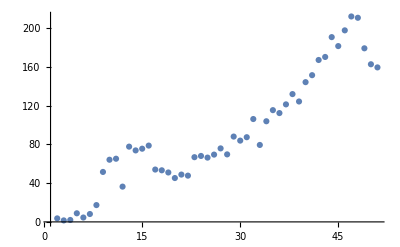

```mathematica
n=1;
Iter=1;
data={};
alldata={};

Do[
n++;
M=RandomReal[{-1,1},{n,n}];
M1=RandomReal[{-1,1},{n^2,n^2}];

bigtime=(Do[Eigensystem@M1;,{iter,1,Iter}]//AbsoluteTiming)[[1]];
smalltime=(Do[Eigensystem@M;,{iter,1,Iter n}]//AbsoluteTiming)[[1]];

AppendTo[alldata,{n,smalltime,bigtime}];
AppendTo[data,{n,bigtime/smalltime}];
,{it,1,50}]
ListPlot[data,PlotRange->All]
```

-13.0619+2.52088 x

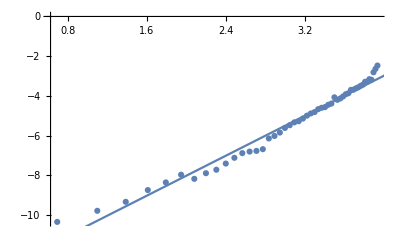

```mathematica
a+b x/.FindFit[Table[{Log@alldata[[i,1]],Log@alldata[[i,2]]},{i,Length@alldata}],a+b x,{a,b},x]
Show[{ListPlot[Table[{Log@alldata[[i,1]],Log@alldata[[i,2]]},{i,Length@alldata}],PlotRange->All],Plot[%,{x,0,5}]}]
```

-13.1223+3.89432 x

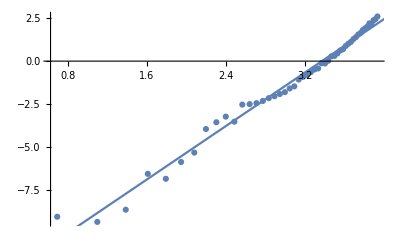

```mathematica
a+b x/.FindFit[Table[{Log@alldata[[i,1]],Log@alldata[[i,3]]},{i,Length@alldata}],a+b x,{a,b},x]
Show[{ListPlot[Table[{Log@alldata[[i,1]],Log@alldata[[i,3]]},{i,Length@alldata}],PlotRange->All],Plot[%,{x,0,5}]}]
```

```mathematica
n=1;
Iter=100;
data0={};

Do[
n++;
M=RandomReal[{-1,1},{n,n}];

time=(Do[Eigensystem@M;,{iter,1,Iter}]//AbsoluteTiming)[[1]];

AppendTo[data0,{n,time/Iter}];
,{it,1,100}]
```

-15.0746+2.20183 x

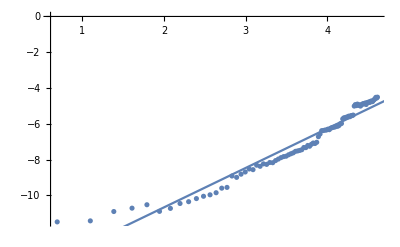

```mathematica
a+b x/.FindFit[Table[{Log@data0[[i,1]],Log@data0[[i,2]]},{i,Length@data0}],a+b x,{a,b},x]
Show[{ListPlot[Table[{Log@data0[[i,1]],Log@data0[[i,2]]},{i,Length@data0}],PlotRange->All],Plot[%,{x,0,5}]}]
```

```mathematica
Do[M[[j+ny (i-1),j+ny (i-1)+nxy]]=N[d[[j+ny (i-1)]]],{i,nx},{j,ny}];
Do[M[[j+ny (i-1)+nxy,j+ny (i-1)]]=N[d[[j+ny (i-1)]]*],{i,nx},{j,ny}];

{e,evec}=Eigensystem[M];

{evecU,evecV}=Partition[evecᵀ,nxy];
f[x_]=(1/(Exp[x/T]+1));
Module[{i2=2,j2=2},
Im@Table[
(hpm[i2,j2,i1,j1,+1]+(μ+h) δ[i1,i2] δ[j1,j2]) Sum[(evecU[[j1+ny (i1-1),k]]*) evecU[[j2+ny (i2-1),k]] f[e[[k]]],{k,Length@e}](*-(hpm[i2,j2,i1,j1,-1]+(μ-h) δ[i1,i2] δ[j1,j2]) Sum[evecV[[j1+ny (i1-1),k]] evecV[[j2+ny (i2-1),k]]* f[e[[k]]],{k,Length@e}]*)
,{j1,ny},{i1,nx}]//MatrixForm
]
```

(0. | -0.000253263
-0.00145052 | 0.)

```mathematica
eps=Table[M[[i,j]] ,{i,nxy},{j,nxy}];
ff=Table[Sum[evec[[k,i]] e[[k]]^3 (evec[[k,j]]*) ,{k,Length@e}],{i,nxy},{j,nxy}];
```

```mathematica
eps.ff-ff.eps//Abs//Max
```

0.0354388

```mathematica
ff=Table[Sum[evec[[k,i]] f@e[[k]] (evec[[k,j]]*),{k,Length@e}],{i,2 nxy},{j,2 nxy}];
M.ff-ff.M//Abs//Max
```

3.9969×10^-15

```mathematica
M.(evecᵀ)-(evecᵀ).DiagonalMatrix[e]//FullSimplify
```

{{0,0},{0,0}}

```mathematica
(evec*).M.(evecᵀ)-DiagonalMatrix[e]//Abs//Max
```

1.08701×10^-14

```mathematica
(ff†)-ff//Abs//Max
```

0.